```mathematica
Graph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,4<->5,3<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,6<->7},VertexCoordinates->{1->{0,0},2->{100,0},3->{0,100},4->{33.33333,33.33333},5->{16.66667,16.66667},6->{66.66666,16.66667},7->{58.33333,8.333333}},PlotLabel->"0 - 4 [1] (1<->2<->3), 5 [2] (1<->4), 6 [2] (2<->4), 7 [2] (2<->5)"]
Graph[{1,2,3,4,5,6,7,8},{1<->2,1<->3,2<->3,3<->4,1<->5,4<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,6<->7,3<->8,5<->8,1<->8,4<->8},VertexCoordinates->{1->{0,0},2->{100,0},3->{0,100},4->{33.33333,33.33333},5->{16.66667,16.66667},6-
>{66.66666,16.66667},7->{58.33333,8.333333},8->{8.333335,58.33334}},PlotLabel->"1 - 4 [1] (1<->2<->3), 5 [2] (1<->4), 6 [2] (2<->4), 7 [2] (2<->5), 8 [2] (3<->5)"]
From 96 down to 72
```

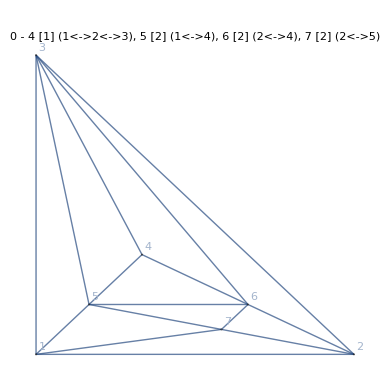

```mathematica
Graph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,4<->5,3<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,6<->7},VertexCoordinates->{1->{0,0},2->{100,0},3->{0,100},4->{33.33333,33.33333},5->{16.66667,16.66667},6->{66.66666,16.66667},7->{58.33333,8.333333}},PlotLabel->"0 - 4 [1] (1<->2<->3), 5 [2] (1<->4), 6 [2] (2<->4), 7 [2] (2<->5)", VertexLabels->"Name"]
```

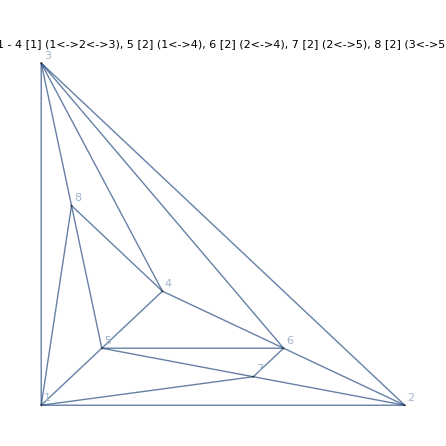

```mathematica
Graph[{1,2,3,4,5,6,7,8},{1<->2,1<->3,2<->3,3<->4,1<->5,4<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,6<->7,3<->8,5<->8,1<->8,4<->8},VertexCoordinates->{1->{0,0},2->{100,0},3->{0,100},4->{33.33333,33.33333},5->{16.66667,16.66667},6->{66.66666,16.66667},7->{58.33333,8.333333},8->{8.333335,58.33334}},PlotLabel->"1 - 4 [1] (1<->2<->3), 5 [2] (1<->4), 6 [2] (2<->4), 7 [2] (2<->5), 8 [2] (3<->5)", VertexLabels->"Name"]
```

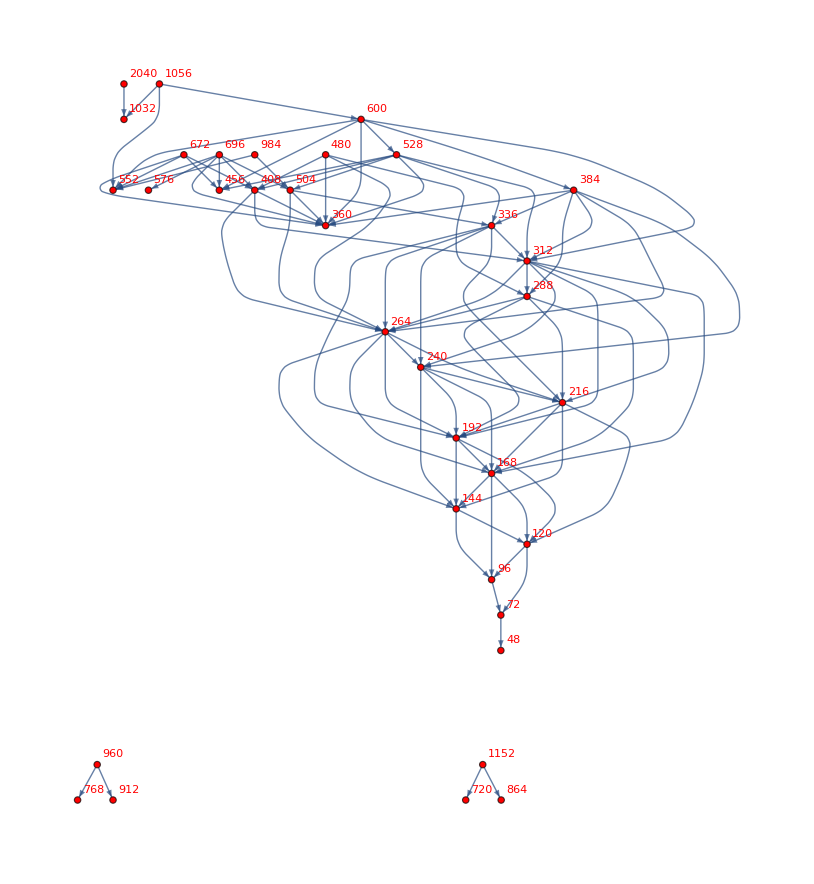

```mathematica
Graph[{96->72,120->72,120->96,72->48,288->168,288->192,288->216,288->264,216->120,216->144,216->168,216->192,384->240,384->264,384->288,384->312,384->336,384->360,144->96,144->120,504->264,504->336,504->360,480->264,480->288,480->360,480->408,312->168,312->192,312->216,312->240,312->264,312->288,336->192,336->216,336->240,336->264,336->312,672->360,672->408,672->456,672->552,264->144,264->168,264->192,264->216,264->240,168->96,168->120,168->144,192->120,192->144,192->168,1056->552,1056->600,1056->1032,696->360,696->408,696->456,696->504,696->552,696->576,528->312,528->336,528->360,528->408,528->456,528->504,240->144,240->168,240->192,240->216,1152->720,1152->864,600->312,600->360,600->384,600->456,600->528,600->552,408->264,408->312,408->360,960->768,960->912,984->504,984->552,2040->1032},VertexLabels->"Name", VertexStyle->Red, VertexLabelStyle->Red]
```

```mathematica
Map[#[[1]]/24->#[[2]]/24&,{96->72,120->72,120->96,72->48,288->168,288->192,288->216,288->264,216->120,216->144,216->168,216->192,384->240,384->264,384->288,384->312,384->336,384->360,144->96,144->120,504->264,504->336,504->360,480->264,480->288,480->360,480->408,312->168,312->192,312->216,312->240,312->264,312->288,336->192,336->216,336->240,336->264,336->312,672->360,672->408,672->456,672->552,264->144,264->168,264->192,264->216,264->240,168->96,168->120,168->144,192->120,192->144,192->168,1056->552,1056->600,1056->1032,696->360,696->408,696->456,696->504,696->552,696->576,528->312,528->336,528->360,528->408,528->456,528->504,240->144,240->168,240->192,240->216,1152->720,1152->864,600->312,600->360,600->384,600->456,600->528,600->552,408->264,408->312,408->360,960->768,960->912,984->504,984->552,2040->1032}]
```

{4→3,5→3,5→4,3→2,12→7,12→8,12→9,12→11,9→5,9→6,9→7,9→8,16→10,16→11,16→12,16→13,16→14,16→15,6→4,6→5,21→11,21→14,21→15,20→11,20→12,20→15,20→17,13→7,13→8,13→9,13→10,13→11,13→12,14→8,14→9,14→10,14→11,14→13,28→15,28→17,28→19,28→23,11→6,11→7,11→8,11→9,11→10,7→4,7→5,7→6,8→5,8→6,8→7,44→23,44→25,44→43,29→15,29→17,29→19,29→21,29→23,29→24,22→13,22→14,22→15,22→17,22→19,22→21,10→6,10→7,10→8,10→9,48→30,48→36,25→13,25→15,25→16,25→19,25→22,25→23,17→11,17→13,17→15,40→32,40→38,41→21,41→23,85→43}

```mathematica
Sort[Tally[Map[#[[1]]/24-#[[2]]/24&,{96->72,120->72,120->96,72->48,288->168,288->192,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,480->360,312->168,312->192,312->216,312->264,312->288,336->216,336->240,336->264,672->408,672->456,672->552,264->144,264->168,264->192,264->240,168->96,168->144,192->168,1056->600,696->408,696->456,696->504,696->552,696->576,528->312,528->336,528->360,528->408,528->456,528->504,240->168}]]]
```

{{1,11},{2,5},{3,6},{4,6},{5,8},{6,3},{7,2},{8,3},{9,3},{10,2},{11,1},{12,1},{19,1}}

```mathematica
Sort[Map[#->{#1*10,0}&,VertexList[Graph[{4->3,5->3,5->4,3->2,12->7,12->8,12->9,12->11,9->5,9->6,9->7,9->8,16->10,16->11,16->12,16->13,16->14,16->15,6->4,6->5,21->11,21->14,21->15,20->11,20->12,20->15,20->17,13->7,13->8,13->9,13->10,13->11,13->12,14->8,14->9,14->10,14->11,14->13,28->15,28->17,28->19,28->23,11->6,11->7,11->8,11->9,11->10,7->4,7->5,7->6,8->5,8->6,8->7,44->23,44->25,44->43,29->15,29->17,29->19,29->21,29->23,29->24,22->13,22->14,22->15,22->17,22->19,22->21,10->6,10->7,10->8,10->9,48->30,48->36,25->13,25->15,25->16,25->19,25->22,25->23,17->11,17->13,17->15,40->32,40->38,41->21,41->23}]]]]
```

{2→{20,0},3→{30,0},4→{40,0},5→{50,0},6→{60,0},7→{70,0},8→{80,0},9→{90,0},10→{100,0},11→{110,0},12→{120,0},13→{130,0},14→{140,0},15→{150,0},16→{160,0},17→{170,0},19→{190,0},20→{200,0},21→{210,0},22→{220,0},23→{230,0},24→{240,0},25→{250,0},28→{280,0},29→{290,0},30→{300,0},32→{320,0},36→{360,0},38→{380,0},40→{400,0},41→{410,0},43→{430,0},44→{440,0},48→{480,0}}

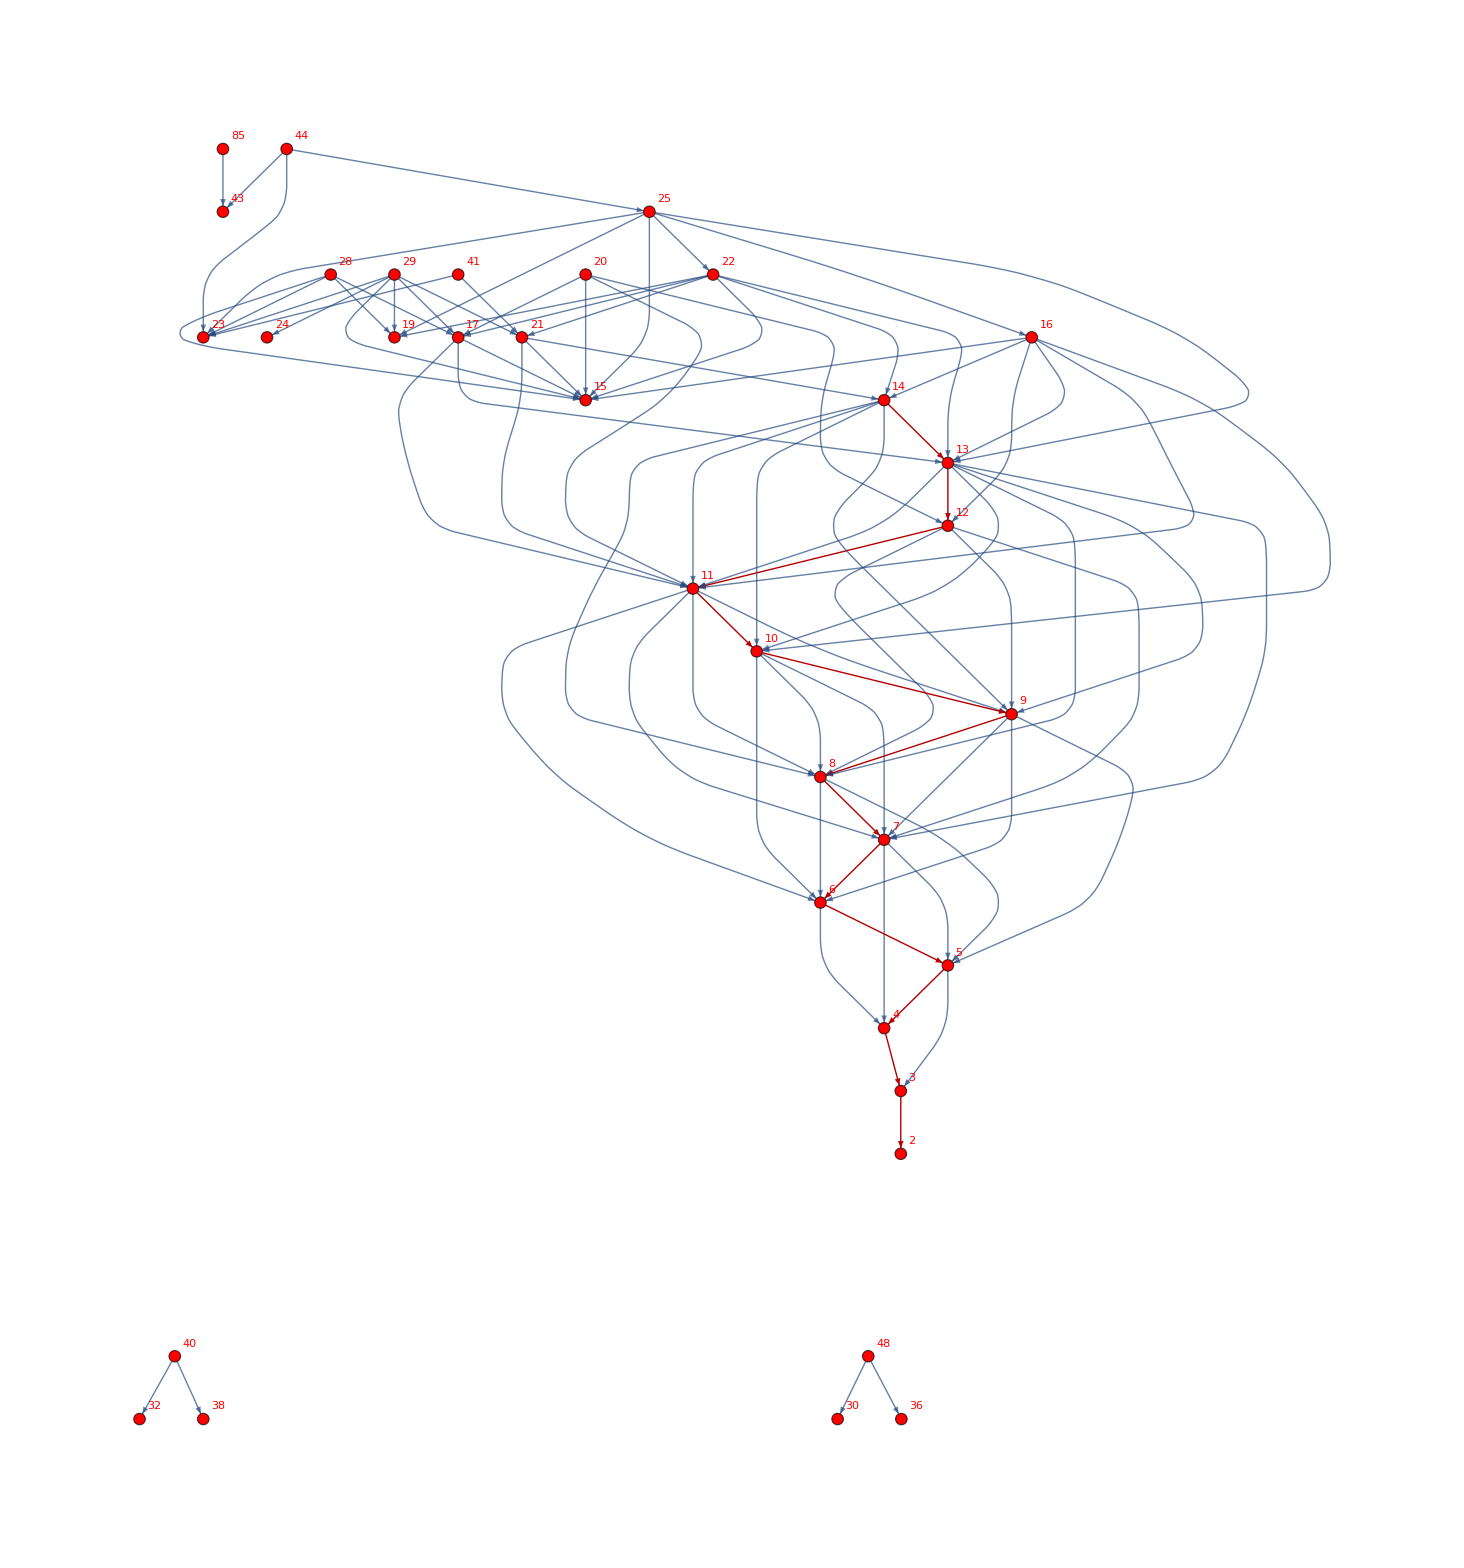

```mathematica
Graph[{4->3,5->3,5->4,3->2,12->7,12->8,12->9,12->11,9->5,9->6,9->7,9->8,16->10,16->11,16->12,16->13,16->14,16->15,6->4,6->5,21->11,21->14,21->15,20->11,20->12,20->15,20->17,13->7,13->8,13->9,13->10,13->11,13->12,14->8,14->9,14->10,14->11,14->13,28->15,28->17,28->19,28->23,11->6,11->7,11->8,11->9,11->10,7->4,7->5,7->6,8->5,8->6,8->7,44->23,44->25,44->43,29->15,29->17,29->19,29->21,29->23,29->24,22->13,22->14,22->15,22->17,22->19,22->21,10->6,10->7,10->8,10->9,48->30,48->36,25->13,25->15,25->16,25->19,25->22,25->23,17->11,17->13,17->15,40->32,40->38,41->21,41->23,85->43}, VertexLabels->"Name",GraphHighlight->{3->2,4->3,5->4,6->5,7->6,8->7,9->8,10->9,14->13,13->12,12->11,11->10}, VertexStyle->Red, VertexLabelStyle->Red]
```

```mathematica
KatzCentrality[Graph[{4->3,5->3,5->4,3->2,12->7,12->8,12->9,12->11,9->5,9->6,9->7,9->8,16->10,16->11,16->12,16->13,16->14,16->15,6->4,6->5,21->11,21->14,20->11,20->12,20->15,20->17,13->7,13->8,13->9,13->10,13->11,13->12,14->8,14->9,14->10,14->11,14->13,28->15,28->17,28->19,28->23,11->6,11->7,11->8,11->9,11->10,7->4,7->5,7->6,8->6,8->7,44->25,29->15,29->17,29->19,29->21,29->23,29->24,22->13,22->14,22->15,22->17,22->19,22->21,10->6,10->7,10->8,10->9,48->30,48->36,25->13,25->15,25->16,25->19,25->22,25->23,17->11,17->13,17->15,40->32,40->38,41->21,41->23}, VertexLabels->"Name"],0.1]
```

{1.5527,1.31265,1.5738,1.13127,1.37184,2.02438,1.96336,1.78487,1.91654,1.92879,1.11,1.5988,1.60841,1.3531,1.7731,1.311,1.,1.411,1.,1.421,1.41,1.,1.1,1.,1.1,1.11,1.,1.1,1.1,1.,1.1,1.1,1.}

```mathematica
Sort[{5->3,4->3,12->7,12->9,12->11,3->2,9->5,9->7,9->8,21->11,16->14,6->5}]
```

{3→2,4→3,5→3,6→5,9→5,9→7,9→8,12→7,12→9,12→11,16→14,21→11}

```mathematica
MatrixForm[AdjacencyMatrix[Graph[{3->2,4->3,5->3,6->5,9->5,9->7,9->8,12->7,12->9,12->11,16->14,21->11}, VertexLabels->"Name"]]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
D:\Users\Willy\Documents\Visual Studio 2013\Projects\GeneratePlanarGraphs\GeneratePlanarGraphs\bin\Release>GeneratePlanarGraphs.exe
4-found 0-minimal:1
5-found 0-minimal:1
6-found 0-minimal:1
96->72
96->72,120->72
7-found 11-minimal:3
96->72,120->72,72->48
96->72,120->72,72->48,288->216
8-found 34-minimal:7
96->72,120->72,72->48,288->216,216->120
96->72,120->72,72->48,288->216,216->120,216->168
96->72,120->72,72->48,288->216,216->120,216->168,384->336
96->72,120->72,72->48,288->168,288->216,216->120,216->168,384->336
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->336
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->336,144->120
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->336,144->120,504->264
9-found 121-minimal:24
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->288,384->336,144->120,504->264
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->288,384->336,144->120,504->264,480->288
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->288,384->336,144->120,504->264,480->264,480->288
96->72,120->72,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->120,504->264,480->264,480->288
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->120,504->264,480->264,480->288
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->216,312->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->240
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96,168->144
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96,168->144
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96,168->144,192->168
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96,168->144,192->168,1056->600
10-found 677-minimal:93
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,480->360,312->168,312->216,312->264,336->216,336->240,336->264,672->408,264->144,264->240,168->96,168->144,192->168,1056->600
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,480->360,312->168,312->216,312->264,336->216,336->240,336->264,672->408,672->456,264->144,264->240,168->96,168->144,192->168,1056->600
96->72,120->72,120->96,72->48,288->168,288->216,288->264,216->120,216->168,216->192,384->240,384->288,384->336,144->96,144->120,504->264,504->336,480->264,480->288,480->360,312->168,312->216,312->264,336->216,336->240,336->264,672->408,672->456,672->552,264->144,264->240,168->96,168->144,192->168,1056->600
```